## Study all the sampled parameters

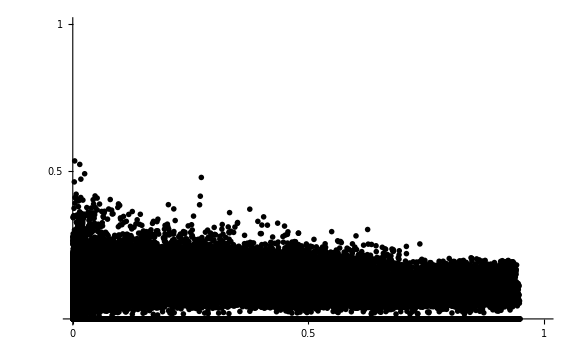

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
transPars=Import["searchingOptimum1/unsaturationSearchingOptimum0Trans.csv"];
pars=Transpose[transPars];
import[n_]:=Import["searchingOptimum1/unsaturationSearchingOptimum"<>ToString[n]<>".csv"];
firstPars=Flatten[ParallelMap[import,Range[15]],1];
pars=Join[pars,firstPars];
transPars=Transpose[pars];
ListPlot[Transpose[{transPars[[15]],transPars[[16]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

```mathematica
ad20index=Reverse[Ordering[transPars[[16]],-20]]
```

{151463,3400,118404,554,156122,28492,69001,59396,9803,127960,150700,89587,3487,76680,76082,27708,68668,46968,69752,131845}

```mathematica
bestPars=pars[[ad20index]][[16]]
```

{15.1371,0.277014,15.5873,153.148,14.0364,5.50897,168.54,0.0078975,8.30193,0.00645858,1.30551,0.0001,0.1,0.1,0.0432747,0.403626,7708,1.04804,0.127624,0.0000468585,0.000777961}

## [S] = 0.1

```mathematica
ClearAll["Global`*"];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t]+k11[t]*kd-kd*x[1][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t],0};

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
bestPars={15.137087450338703,0.2770135173971178,15.587297258962813,153.14831264861263,14.036431748093168,5.508973549338161,168.53950326875648,0.007897502629053513,8.301928387552797,0.006458580126609296,1.3055087385838648,0.0001,0.1,0.1,0.04327472675432927,0.40362605906067556,7708,1.0480424869319862,0.12762403293516397,0.00004685846626983347,0.0007779614355976305};

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[];

totK=0.0001;totP=0.1;totS=0.1;
stepNum=5;
sampleSize=1000;

maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];
adToUsPars={};
ts={};
For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*6-3);

Block[{tPer,step,us,ad,x4,sol,i},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,{totT,us,ad,num}];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];

usVsAd=Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}];
altitude= Log10[transAdToUsPars[[1]]];
colorf=Blend[{{Min[altitude],Cyan},{Max[altitude],Magenta}},#]&;
plotLegend[{min_,max_},n_,col_]:=Graphics[MapIndexed[{{col[#1],Rectangle[{0,#2[[1]]-1},{1,#2[[1]]}]},{Black,Text[NumberForm[N@#1,{4,2}],{4,#2[[1]]-.5},{1,0}]}}&,Rescale[Range[n],{1,n},{min,max}]],Frame->False,FrameTicks->None,PlotRangePadding->.5];

vsPlot=Graphics[MapThread[{colorf[#1],{PointSize[Large],Point[#2]}}&,{altitude,usVsAd}],Axes->True,AspectRatio->1,PlotRange->{{0,1},{0,1}},Ticks->{{0,0.5,1}, {0.5,1}},PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
leg=plotLegend[Through[{Min,Max}[altitude]],9,colorf];
legTxt=Graphics[Text[StyleForm["Log_10([T])",FontSize->14,FontWeight->"Bold"]]];
pLeg=Grid[{{Show[vsPlot,ImageSize->{Automatic,600}],Grid[{{Show[legTxt,ImageSize->{100,50}]},{Show[leg,ImageSize->{100,Automatic}]}}]}}];
Export["searchedOptimum1/searchingOptimumUnsaturation16S01.eps",pLeg];
Export["searchedOptimum1/searchingOptimumUnsaturation16S01.pdf",pLeg];
```

```mathematica
Print[pLeg]
```

```mathematica
maxUsIndex=Reverse[Ordering[transAdToUsPars[[2]],-1]];
maxAdIndex=Reverse[Ordering[transAdToUsPars[[3]],-1]];

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
stepNum=5;
maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];totT=adToUsPars[[maxUsIndex]][[1]][[1]];
Block[{tPer,step,k11,ts,sol,ssthreshold},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[(Norm[df]<ssthreshold),{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol]/totS;k11t=Evaluate[(k11[ts-0.001])/.sol];
];
fittedHill=FindFit[Transpose@{k11t,x4},a+(b-a)*hillK/(hillK+x^(-n)),{a,b,hillK,n},x]
usPlot=Show[LogLinearPlot[a+(b-a)*hillK/(hillK+x^(-n))/.fittedHill,{x,10^-4,10},(*Ticks->{Automatic,{0,0.5,1}},*) PlotRange->{-0.05,1.05}, AxesLabel->{"[K]","[S_p]/[S_tot]"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}],ListLogLinearPlot[Transpose@{k11t,x4},PlotTheme->"Monochrome",PlotMarkers->{Automatic,24}],(*Text["n=1.5746",{0.65,0.45}],*)
PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
Export["searchedOptimum1/searchingOptimumUnsaturation16S01Us.eps",usPlot];
Export["searchedOptimum1/searchingOptimumUnsaturation16S01Us.pdf",usPlot];
```

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];totT=adToUsPars[[maxAdIndex]][[1]][[1]];
Block[{tPer,step,k11,ssthreshold},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.85,0.85}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,0.01};
stepNum=4;
maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];totT=adToUsPars[[maxAdIndex]][[1]][[1]];
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->5*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Show[Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.6,0.15}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large],Plot[{{k11[t]}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.85,0.15}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Dashed,Thickness[0.007]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]]
```

```mathematica
input=LogPlot[{{k11[t]}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.85,0.15}],PlotTheme->"Monochrome", PlotStyle->{Blue,Dashed,Thickness[0.007]},Ticks->{},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{True,True,False,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}];
output=Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.6,0.15}],PlotRange->{0,1},PlotStyle->{Darker[Green],Thickness[0.01]},Ticks->{0,0.5,1},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,(*Axes->False,*)Frame->{False,False,False,True},FrameTicks->{None,None,None,{0,0.5,1}},FrameStyle->{Automatic,Automatic,Automatic,Darker[Green]}];
adPlot=Overlay[{output,input}]
Export["searchedOptimum1/searchingOptimumUnsaturation16S01Ad.eps",adPlot];
Export["searchedOptimum1/searchingOptimumUnsaturation16S01Ad.pdf",adPlot];
```

## [S] = 0.2

```mathematica
ClearAll["Global`*"];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t]+k11[t]*kd-kd*x[1][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t],0};

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
bestPars={15.137087450338703,0.2770135173971178,15.587297258962813,153.14831264861263,14.036431748093168,5.508973549338161,168.53950326875648,0.007897502629053513,8.301928387552797,0.006458580126609296,1.3055087385838648,0.0001,0.1,0.1,0.04327472675432927,0.40362605906067556,7708,1.0480424869319862,0.12762403293516397,0.00004685846626983347,0.0007779614355976305};

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[];

totK=0.0001;totP=0.1;totS=0.2;
stepNum=5;
sampleSize=1000;

maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];
adToUsPars={};
ts={};
For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*6-3);

Block[{tPer,step,us,ad,x4,sol,i},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,{totT,us,ad,num}];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];

usVsAd=Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}];
altitude= Log10[transAdToUsPars[[1]]];
colorf=Blend[{{Min[altitude],Cyan},{Max[altitude],Magenta}},#]&;
plotLegend[{min_,max_},n_,col_]:=Graphics[MapIndexed[{{col[#1],Rectangle[{0,#2[[1]]-1},{1,#2[[1]]}]},{Black,Text[NumberForm[N@#1,{4,2}],{4,#2[[1]]-.5},{1,0}]}}&,Rescale[Range[n],{1,n},{min,max}]],Frame->False,FrameTicks->None,PlotRangePadding->.5];

vsPlot=Graphics[MapThread[{colorf[#1],{PointSize[Large],Point[#2]}}&,{altitude,usVsAd}],Axes->True,AspectRatio->1,PlotRange->{{0,1},{0,1}},Ticks->{{0,0.5,1}, {0.5,1}},PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
leg=plotLegend[Through[{Min,Max}[altitude]],9,colorf];
legTxt=Graphics[Text[StyleForm["Log_10([T])",FontSize->14,FontWeight->"Bold"]]];
pLeg=Grid[{{Show[vsPlot,ImageSize->{Automatic,600}],Grid[{{Show[legTxt,ImageSize->{100,50}]},{Show[leg,ImageSize->{100,Automatic}]}}]}}];
Export["searchedOptimum1/searchingOptimumUnsaturation16S02.eps",pLeg];
Export["searchedOptimum1/searchingOptimumUnsaturation16S02.pdf",pLeg];
```

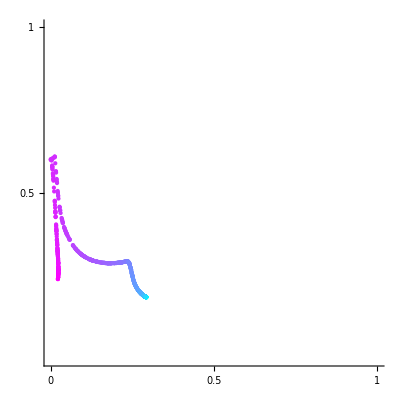
-Graphics- | -Graphics-
-Graphics-

```mathematica
Print[pLeg]
```

```mathematica
maxUsIndex=Reverse[Ordering[transAdToUsPars[[2]],-1]];
maxAdIndex=Reverse[Ordering[transAdToUsPars[[3]],-1]];

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
stepNum=5;
maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];totT=adToUsPars[[maxUsIndex]][[1]][[1]];
Block[{tPer,step,k11,ts,sol,ssthreshold},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[(Norm[df]<ssthreshold),{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol]/totS;k11t=Evaluate[(k11[ts-0.001])/.sol];
];
fittedHill=FindFit[Transpose@{k11t,x4},a+(b-a)*hillK/(hillK+x^(-n)),{a,b,hillK,n},x]
usPlot=Show[LogLinearPlot[a+(b-a)*hillK/(hillK+x^(-n))/.fittedHill,{x,10^-4,10},(*Ticks->{Automatic,{0,0.5,1}},*) PlotRange->{-0.05,1.05}, AxesLabel->{"[K]","[S_p]/[S_tot]"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}],ListLogLinearPlot[Transpose@{k11t,x4},PlotTheme->"Monochrome",PlotMarkers->{Automatic,24}],(*Text["n=1.5746",{0.65,0.45}],*)
PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
Export["searchedOptimum1/searchingOptimumUnsaturation16S02Us.eps",usPlot];
Export["searchedOptimum1/searchingOptimumUnsaturation16S02Us.pdf",usPlot];
```

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];totT=adToUsPars[[maxAdIndex]][[1]][[1]];
Block[{tPer,step,k11,ssthreshold},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.85,0.85}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,0.01};
stepNum=4;
maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];totT=adToUsPars[[maxAdIndex]][[1]][[1]];
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->5*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Show[Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.6,0.15}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large],Plot[{{k11[t]}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.85,0.15}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Dashed,Thickness[0.007]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]]
```

```mathematica
input=LogPlot[{{k11[t]}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.85,0.15}],PlotTheme->"Monochrome", PlotStyle->{Blue,Dashed,Thickness[0.007]},Ticks->{},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{True,True,False,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}];
output=Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.6,0.15}],PlotRange->{0,1},PlotStyle->{Darker[Green],Thickness[0.01]},Ticks->{0,0.5,1},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,(*Axes->False,*)Frame->{False,False,False,True},FrameTicks->{None,None,None,{0,0.5,1}},FrameStyle->{Automatic,Automatic,Automatic,Darker[Green]}];
adPlot=Overlay[{output,input}]
Export["searchedOptimum1/searchingOptimumUnsaturation16S02Ad.eps",adPlot];
Export["searchedOptimum1/searchingOptimumUnsaturation16S02Ad.pdf",adPlot];
```

## [S] = 0.5

```mathematica
ClearAll["Global`*"];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t]+k11[t]*kd-kd*x[1][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t],0};

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
bestPars={15.137087450338703,0.2770135173971178,15.587297258962813,153.14831264861263,14.036431748093168,5.508973549338161,168.53950326875648,0.007897502629053513,8.301928387552797,0.006458580126609296,1.3055087385838648,0.0001,0.1,0.1,0.04327472675432927,0.40362605906067556,7708,1.0480424869319862,0.12762403293516397,0.00004685846626983347,0.0007779614355976305};

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[];

totK=0.0001;totP=0.1;totS=0.5;
stepNum=5;
sampleSize=1000;

maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];
adToUsPars={};
ts={};
For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*6-3);

Block[{tPer,step,us,ad,x4,sol,i},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,{totT,us,ad,num}];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];

usVsAd=Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}];
altitude= Log10[transAdToUsPars[[1]]];
colorf=Blend[{{Min[altitude],Cyan},{Max[altitude],Magenta}},#]&;
plotLegend[{min_,max_},n_,col_]:=Graphics[MapIndexed[{{col[#1],Rectangle[{0,#2[[1]]-1},{1,#2[[1]]}]},{Black,Text[NumberForm[N@#1,{4,2}],{4,#2[[1]]-.5},{1,0}]}}&,Rescale[Range[n],{1,n},{min,max}]],Frame->False,FrameTicks->None,PlotRangePadding->.5];

vsPlot=Graphics[MapThread[{colorf[#1],{PointSize[Large],Point[#2]}}&,{altitude,usVsAd}],Axes->True,AspectRatio->1,PlotRange->{{0,1},{0,1}},Ticks->{{0,0.5,1}, {0.5,1}},PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
leg=plotLegend[Through[{Min,Max}[altitude]],9,colorf];
legTxt=Graphics[Text[StyleForm["Log_10([T])",FontSize->14,FontWeight->"Bold"]]];
pLeg=Grid[{{Show[vsPlot,ImageSize->{Automatic,600}],Grid[{{Show[legTxt,ImageSize->{100,50}]},{Show[leg,ImageSize->{100,Automatic}]}}]}}];
Export["searchedOptimum1/searchingOptimumUnsaturation16S05.eps",pLeg];
Export["searchedOptimum1/searchingOptimumUnsaturation16S05.pdf",pLeg];
```

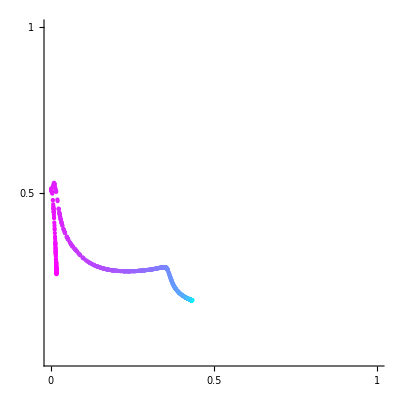
-Graphics- | -Graphics-
-Graphics-

```mathematica
Print[pLeg]
```

{a→-0.00070613,b→0.791103,hillK→17.6015,n→1.25368}

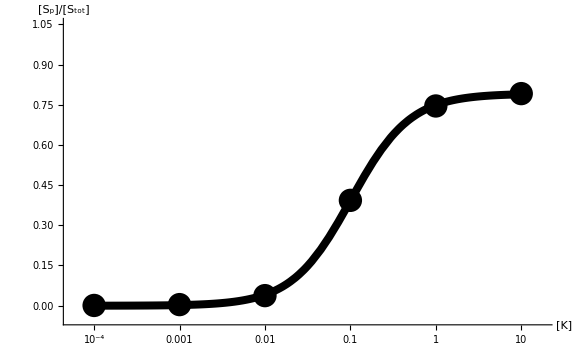

```mathematica
maxUsIndex=Reverse[Ordering[transAdToUsPars[[2]],-1]];
maxAdIndex=Reverse[Ordering[transAdToUsPars[[3]],-1]];

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
stepNum=5;
maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];totT=adToUsPars[[maxUsIndex]][[1]][[1]];
Block[{tPer,step,k11,ts,sol,ssthreshold},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[(Norm[df]<ssthreshold),{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol]/totS;k11t=Evaluate[(k11[ts-0.001])/.sol];
];
fittedHill=FindFit[Transpose@{k11t,x4},a+(b-a)*hillK/(hillK+x^(-n)),{a,b,hillK,n},x]
usPlot=Show[LogLinearPlot[a+(b-a)*hillK/(hillK+x^(-n))/.fittedHill,{x,10^-4,10},(*Ticks->{Automatic,{0,0.5,1}},*) PlotRange->{-0.05,1.05}, AxesLabel->{"[K]","[S_p]/[S_tot]"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}],ListLogLinearPlot[Transpose@{k11t,x4},PlotTheme->"Monochrome",PlotMarkers->{Automatic,24}],(*Text["n=1.5746",{0.65,0.45}],*)
PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
Export["searchedOptimum1/searchingOptimumUnsaturation16S05Us.eps",usPlot];
Export["searchedOptimum1/searchingOptimumUnsaturation16S05Us.pdf",usPlot];
```

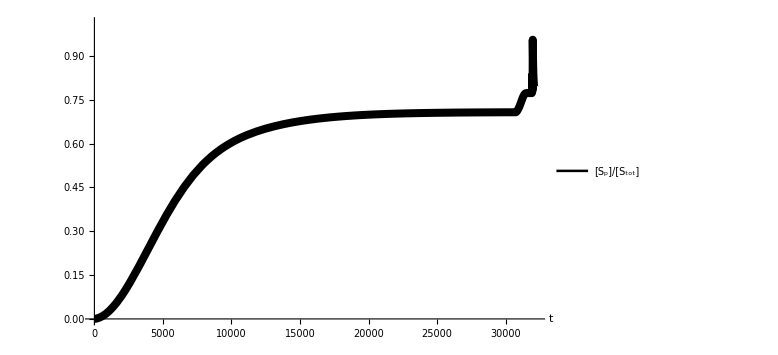

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];totT=adToUsPars[[maxAdIndex]][[1]][[1]];
Block[{tPer,step,k11,ssthreshold},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.85,0.85}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

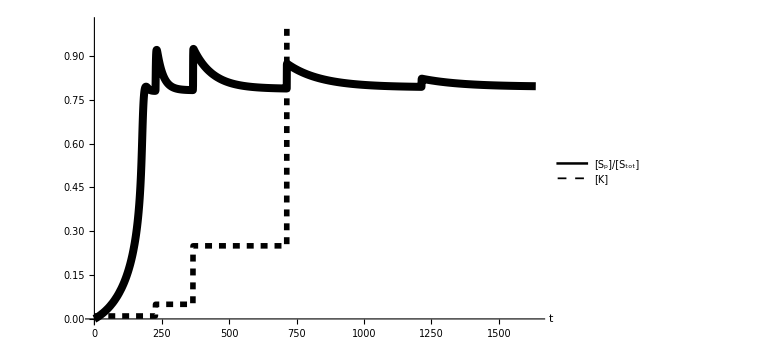

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,0.01};
stepNum=4;
maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];totT=adToUsPars[[maxAdIndex]][[1]][[1]];
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->5*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Show[Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.6,0.15}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large],Plot[{{k11[t]}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.85,0.15}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Dashed,Thickness[0.007]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]]
```

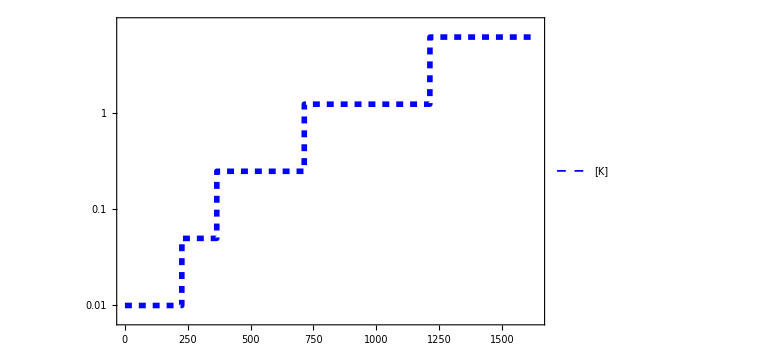

```mathematica
input=LogPlot[{{k11[t]}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.85,0.15}],PlotTheme->"Monochrome", PlotStyle->{Blue,Dashed,Thickness[0.007]},Ticks->{},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{True,True,False,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}]
```

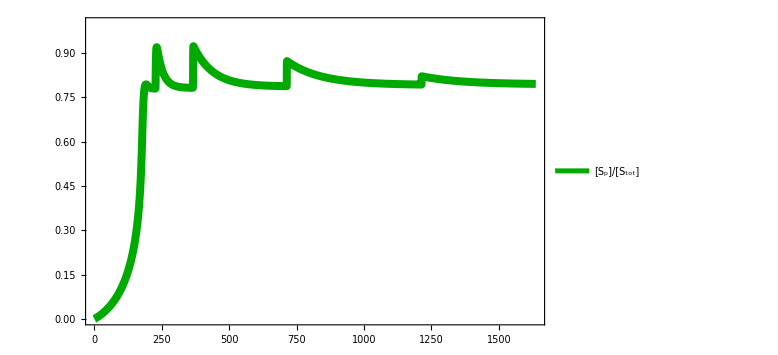

```mathematica
output=Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.6,0.15}],PlotRange->{0,1},PlotStyle->{Darker[Green],Thickness[0.01]},Ticks->{0,0.5,1},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,(*Axes->False,*)Frame->{False,False,False,True},FrameTicks->{None,None,None,{0,0.5,1}},FrameStyle->{Automatic,Automatic,Automatic,Darker[Green]}]
```

```mathematica
adPlot=Overlay[{output,input}]
Export["searchedOptimum1/searchingOptimumUnsaturation16S05Ad.eps",adPlot];
Export["searchedOptimum1/searchingOptimumUnsaturation16S05Ad.pdf",adPlot];
```

-Graphics--Graphics-

## [S] = 1

```mathematica
ClearAll["Global`*"];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t]+k11[t]*kd-kd*x[1][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t],0};

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
```

```mathematica
bestPars={15.137087450338703,0.2770135173971178,15.587297258962813,153.14831264861263,14.036431748093168,5.508973549338161,168.53950326875648,0.007897502629053513,8.301928387552797,0.006458580126609296,1.3055087385838648,0.0001,0.1,0.1,0.04327472675432927,0.40362605906067556,7708,1.0480424869319862,0.12762403293516397,0.00004685846626983347,0.0007779614355976305};
```

```mathematica
SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[];

totK=0.0001;totP=0.1;totS=1;
stepNum=5;
sampleSize=1000;

maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];
adToUsPars={};
ts={};
For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*6-3);

Block[{tPer,step,us,ad,x4,sol,i},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,{totT,us,ad,num}];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];

usVsAd=Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}];
altitude= Log10[transAdToUsPars[[1]]];
colorf=Blend[{{Min[altitude],Cyan},{Max[altitude],Magenta}},#]&;
plotLegend[{min_,max_},n_,col_]:=Graphics[MapIndexed[{{col[#1],Rectangle[{0,#2[[1]]-1},{1,#2[[1]]}]},{Black,Text[NumberForm[N@#1,{4,2}],{4,#2[[1]]-.5},{1,0}]}}&,Rescale[Range[n],{1,n},{min,max}]],Frame->False,FrameTicks->None,PlotRangePadding->.5];

vsPlot=Graphics[MapThread[{colorf[#1],{PointSize[Large],Point[#2]}}&,{altitude,usVsAd}],Axes->True,AspectRatio->1,PlotRange->{{0,1},{0,1}},Ticks->{{0,0.5,1}, {0.5,1}},PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
leg=plotLegend[Through[{Min,Max}[altitude]],9,colorf];
legTxt=Graphics[Text[StyleForm["Log_10([T])",FontSize->14,FontWeight->"Bold"]]];
pLeg=Grid[{{Show[vsPlot,ImageSize->{Automatic,600}],Grid[{{Show[legTxt,ImageSize->{100,50}]},{Show[leg,ImageSize->{100,Automatic}]}}]}}];
Export["searchedOptimum1/searchingOptimumUnsaturation16S1.eps",pLeg];
Export["searchedOptimum1/searchingOptimumUnsaturation16S1.pdf",pLeg];
```

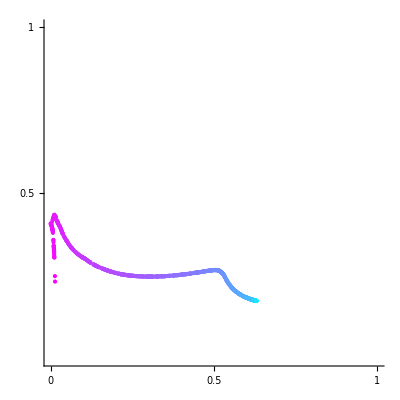
-Graphics- | -Graphics-
-Graphics-

```mathematica
Print[pLeg]
```

```mathematica
maxUsIndex=Reverse[Ordering[transAdToUsPars[[2]],-1]]
```

{79}

```mathematica
maxAdIndex=Reverse[Ordering[transAdToUsPars[[3]],-1]]
```

{648}

{a→0.00029536,b→0.87087,hillK→76.8201,n→1.5746}

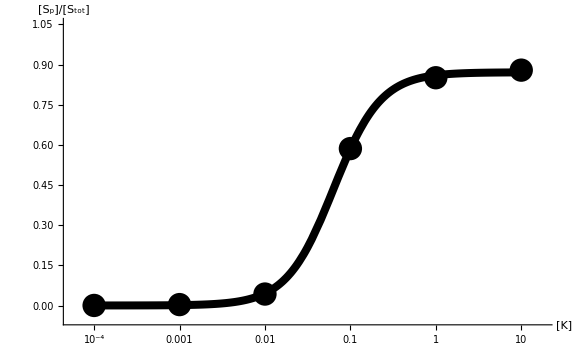

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
stepNum=5;
maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];totT=adToUsPars[[maxUsIndex]][[1]][[1]];
Block[{tPer,step,k11,ts,sol,ssthreshold},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[(Norm[df]<ssthreshold),{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol]/totS;k11t=Evaluate[(k11[ts-0.001])/.sol];
];
fittedHill=FindFit[Transpose@{k11t,x4},a+(b-a)*hillK/(hillK+x^(-n)),{a,b,hillK,n},x]
usPlot=Show[LogLinearPlot[a+(b-a)*hillK/(hillK+x^(-n))/.fittedHill,{x,10^-4,10},(*Ticks->{Automatic,{0,0.5,1}},*) PlotRange->{-0.05,1.05}, AxesLabel->{"[K]","[S_p]/[S_tot]"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}],ListLogLinearPlot[Transpose@{k11t,x4},PlotTheme->"Monochrome",PlotMarkers->{Automatic,24}],(*Text["n=1.5746",{0.65,0.45}],*)
PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
Export["searchedOptimum1/searchingOptimumUnsaturation16P1Us.eps",usPlot];
Export["searchedOptimum1/searchingOptimumUnsaturation16P1Us.pdf",usPlot];
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 55859.1 and t = 55881.3.

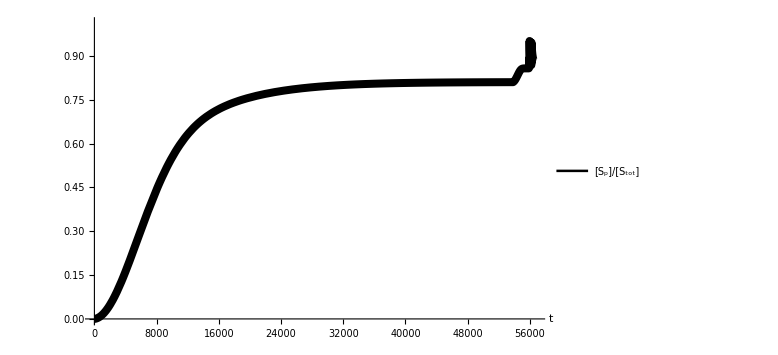

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];totT=adToUsPars[[maxAdIndex]][[1]][[1]];
Block[{tPer,step,k11,ssthreshold},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.85,0.85}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

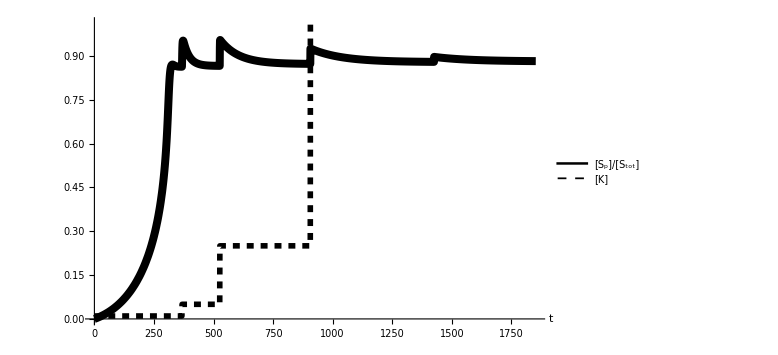

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,0.01};
stepNum=4;
maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];totT=adToUsPars[[maxAdIndex]][[1]][[1]];
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->5*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Show[Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.6,0.15}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large],Plot[{{k11[t]}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.85,0.15}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Dashed,Thickness[0.007]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]]
```

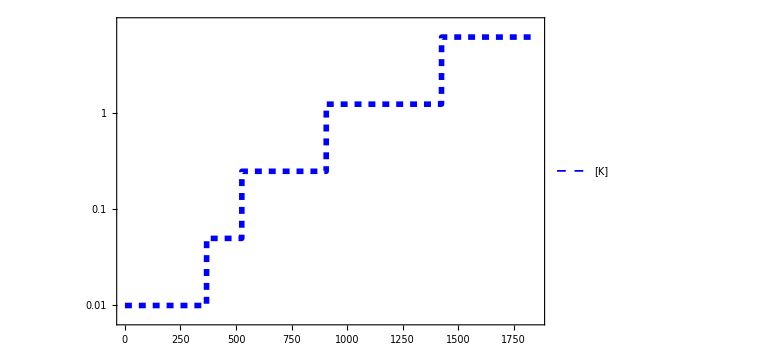

```mathematica
input=LogPlot[{{k11[t]}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.85,0.15}],PlotTheme->"Monochrome", PlotStyle->{Blue,Dashed,Thickness[0.007]},Ticks->{},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{True,True,False,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}]
```

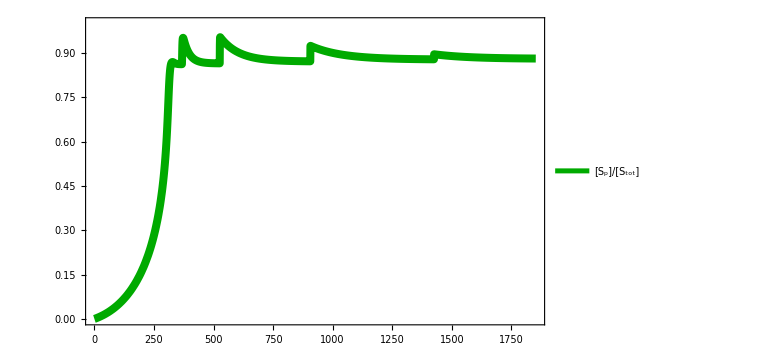

```mathematica
output=Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.6,0.15}],PlotRange->{0,1},PlotStyle->{Darker[Green],Thickness[0.01]},Ticks->{0,0.5,1},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,(*Axes->False,*)Frame->{False,False,False,True},FrameTicks->{None,None,None,{0,0.5,1}},FrameStyle->{Automatic,Automatic,Automatic,Darker[Green]}]
```

```mathematica
adPlot=Overlay[{output,input}]
Export["searchedOptimum1/searchingOptimumUnsaturation16P1Ad.eps",adPlot];
Export["searchedOptimum1/searchingOptimumUnsaturation16P1Ad.pdf",adPlot];
```

-Graphics--Graphics-

## [S] = 2

```mathematica
ClearAll["Global`*"];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t]+k11[t]*kd-kd*x[1][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t],0};

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
bestPars={15.137087450338703,0.2770135173971178,15.587297258962813,153.14831264861263,14.036431748093168,5.508973549338161,168.53950326875648,0.007897502629053513,8.301928387552797,0.006458580126609296,1.3055087385838648,0.0001,0.1,0.1,0.04327472675432927,0.40362605906067556,7708,1.0480424869319862,0.12762403293516397,0.00004685846626983347,0.0007779614355976305};

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[];

totK=0.0001;totP=0.1;totS=2;
stepNum=5;
sampleSize=1000;

maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];
adToUsPars={};
ts={};
For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*6-3);

Block[{tPer,step,us,ad,x4,sol,i},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,{totT,us,ad,num}];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];

usVsAd=Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}];
altitude= Log10[transAdToUsPars[[1]]];
colorf=Blend[{{Min[altitude],Cyan},{Max[altitude],Magenta}},#]&;
plotLegend[{min_,max_},n_,col_]:=Graphics[MapIndexed[{{col[#1],Rectangle[{0,#2[[1]]-1},{1,#2[[1]]}]},{Black,Text[NumberForm[N@#1,{4,2}],{4,#2[[1]]-.5},{1,0}]}}&,Rescale[Range[n],{1,n},{min,max}]],Frame->False,FrameTicks->None,PlotRangePadding->.5];

vsPlot=Graphics[MapThread[{colorf[#1],{PointSize[Large],Point[#2]}}&,{altitude,usVsAd}],Axes->True,AspectRatio->1,PlotRange->{{0,1},{0,1}},Ticks->{{0,0.5,1}, {0.5,1}},PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
leg=plotLegend[Through[{Min,Max}[altitude]],9,colorf];
legTxt=Graphics[Text[StyleForm["Log_10([T])",FontSize->14,FontWeight->"Bold"]]];
pLeg=Grid[{{Show[vsPlot,ImageSize->{Automatic,600}],Grid[{{Show[legTxt,ImageSize->{100,50}]},{Show[leg,ImageSize->{100,Automatic}]}}]}}];
Export["searchedOptimum1/searchingOptimumUnsaturation16S2.eps",pLeg];
Export["searchedOptimum1/searchingOptimumUnsaturation16S2.pdf",pLeg];
```

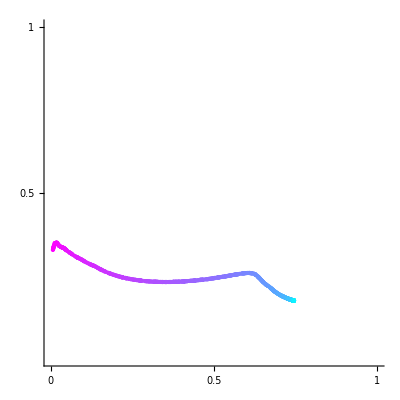
-Graphics- | -Graphics-
-Graphics-

```mathematica
Print[pLeg]
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 153.454 and t = 153.493.

{a→0.00136514,b→0.929204,hillK→321.534,n→1.83043}

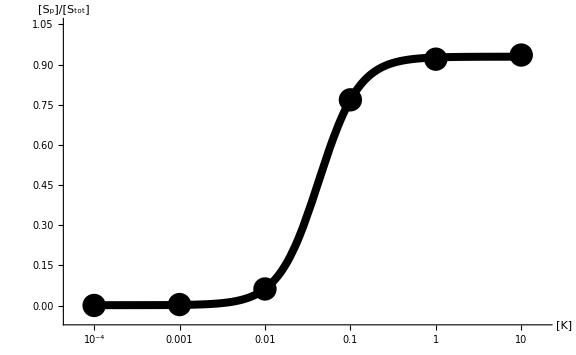

```mathematica
maxUsIndex=Reverse[Ordering[transAdToUsPars[[2]],-1]];
maxAdIndex=Reverse[Ordering[transAdToUsPars[[3]],-1]];

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
stepNum=5;
maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];totT=adToUsPars[[maxUsIndex]][[1]][[1]];
Block[{tPer,step,k11,ts,sol,ssthreshold},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[(Norm[df]<ssthreshold),{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol]/totS;k11t=Evaluate[(k11[ts-0.001])/.sol];
];
fittedHill=FindFit[Transpose@{k11t,x4},a+(b-a)*hillK/(hillK+x^(-n)),{a,b,hillK,n},x]
usPlot=Show[LogLinearPlot[a+(b-a)*hillK/(hillK+x^(-n))/.fittedHill,{x,10^-4,10},(*Ticks->{Automatic,{0,0.5,1}},*) PlotRange->{-0.05,1.05}, AxesLabel->{"[K]","[S_p]/[S_tot]"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}],ListLogLinearPlot[Transpose@{k11t,x4},PlotTheme->"Monochrome",PlotMarkers->{Automatic,24}],(*Text["n=1.5746",{0.65,0.45}],*)
PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
Export["searchedOptimum1/searchingOptimumUnsaturation16S2Us.eps",usPlot];
Export["searchedOptimum1/searchingOptimumUnsaturation16S2Us.pdf",usPlot];
```

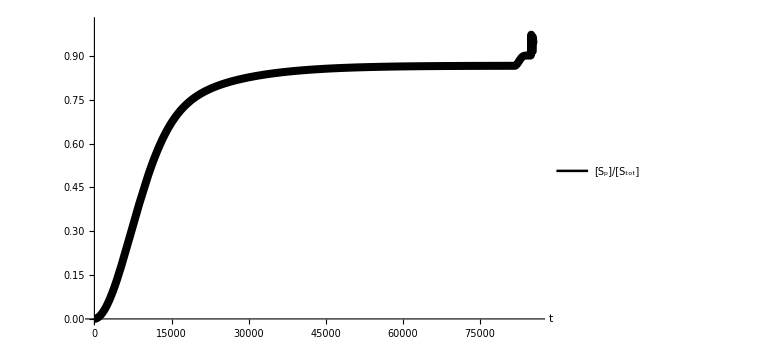

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];totT=adToUsPars[[maxAdIndex]][[1]][[1]];
Block[{tPer,step,k11,ssthreshold},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.85,0.85}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

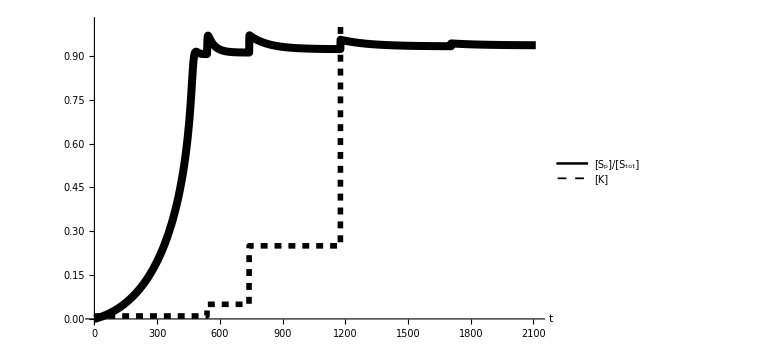

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,0.01};
stepNum=4;
maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];totT=adToUsPars[[maxAdIndex]][[1]][[1]];
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->5*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Show[Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.6,0.15}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large],Plot[{{k11[t]}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.85,0.15}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Dashed,Thickness[0.007]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]]
```

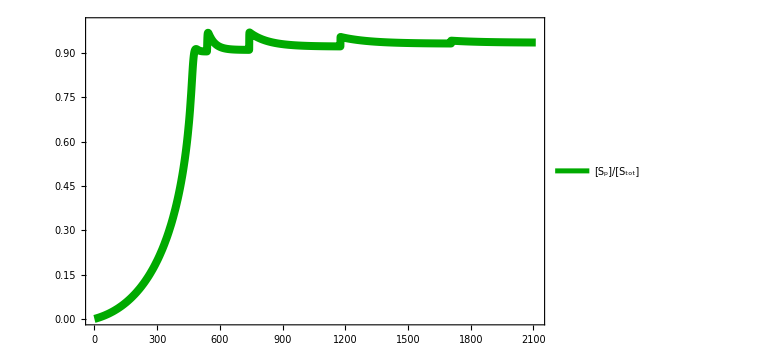
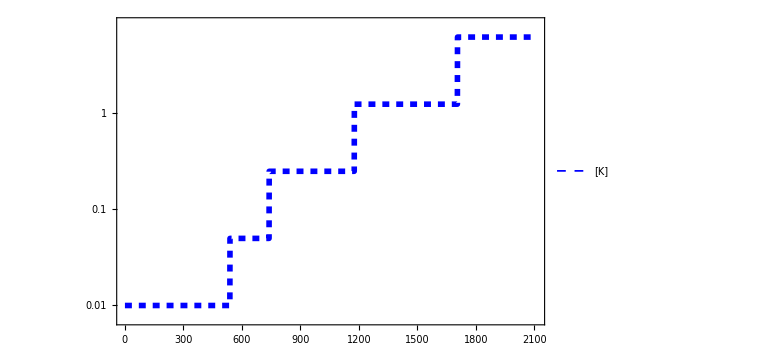

```mathematica
input=LogPlot[{{k11[t]}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.85,0.15}],PlotTheme->"Monochrome", PlotStyle->{Blue,Dashed,Thickness[0.007]},Ticks->{},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{True,True,False,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}];
output=Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.6,0.15}],PlotRange->{0,1},PlotStyle->{Darker[Green],Thickness[0.01]},Ticks->{0,0.5,1},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,(*Axes->False,*)Frame->{False,False,False,True},FrameTicks->{None,None,None,{0,0.5,1}},FrameStyle->{Automatic,Automatic,Automatic,Darker[Green]}];
adPlot=Overlay[{output,input}]
Export["searchedOptimum1/searchingOptimumUnsaturation16S2Ad.eps",adPlot];
Export["searchedOptimum1/searchingOptimumUnsaturation16S2Ad.pdf",adPlot];
```

## [S] = 5

```mathematica
ClearAll["Global`*"];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t]+k11[t]*kd-kd*x[1][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t],0};

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
bestPars={15.137087450338703,0.2770135173971178,15.587297258962813,153.14831264861263,14.036431748093168,5.508973549338161,168.53950326875648,0.007897502629053513,8.301928387552797,0.006458580126609296,1.3055087385838648,0.0001,0.1,0.1,0.04327472675432927,0.40362605906067556,7708,1.0480424869319862,0.12762403293516397,0.00004685846626983347,0.0007779614355976305};

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[];

totK=0.0001;totP=0.1;totS=5;
stepNum=5;
sampleSize=1000;

maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];
adToUsPars={};
ts={};
For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*6-3);

Block[{tPer,step,us,ad,x4,sol,i},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,{totT,us,ad,num}];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];

usVsAd=Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}];
altitude= Log10[transAdToUsPars[[1]]];
colorf=Blend[{{Min[altitude],Cyan},{Max[altitude],Magenta}},#]&;
plotLegend[{min_,max_},n_,col_]:=Graphics[MapIndexed[{{col[#1],Rectangle[{0,#2[[1]]-1},{1,#2[[1]]}]},{Black,Text[NumberForm[N@#1,{4,2}],{4,#2[[1]]-.5},{1,0}]}}&,Rescale[Range[n],{1,n},{min,max}]],Frame->False,FrameTicks->None,PlotRangePadding->.5];

vsPlot=Graphics[MapThread[{colorf[#1],{PointSize[Large],Point[#2]}}&,{altitude,usVsAd}],Axes->True,AspectRatio->1,PlotRange->{{0,1},{0,1}},Ticks->{{0,0.5,1}, {0.5,1}},PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
leg=plotLegend[Through[{Min,Max}[altitude]],9,colorf];
legTxt=Graphics[Text[StyleForm["Log_10([T])",FontSize->14,FontWeight->"Bold"]]];
pLeg=Grid[{{Show[vsPlot,ImageSize->{Automatic,600}],Grid[{{Show[legTxt,ImageSize->{100,50}]},{Show[leg,ImageSize->{100,Automatic}]}}]}}];
Export["searchedOptimum1/searchingOptimumUnsaturation16S5.eps",pLeg];
Export["searchedOptimum1/searchingOptimumUnsaturation16S5.pdf",pLeg];
```

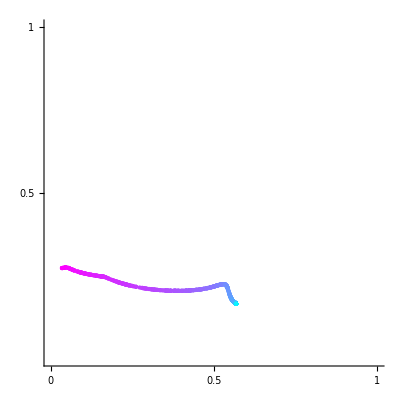
-Graphics- | -Graphics-
-Graphics-

```mathematica
Print[pLeg]
```

```mathematica
maxUsIndex=Reverse[Ordering[transAdToUsPars[[2]],-1]];
maxAdIndex=Reverse[Ordering[transAdToUsPars[[3]],-1]];

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
stepNum=5;
maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];totT=adToUsPars[[maxUsIndex]][[1]][[1]];
Block[{tPer,step,k11,ts,sol,ssthreshold},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[(Norm[df]<ssthreshold),{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol]/totS;k11t=Evaluate[(k11[ts-0.001])/.sol];
];
fittedHill=FindFit[Transpose@{k11t,x4},a+(b-a)*hillK/(hillK+x^(-n)),{a,b,hillK,n},x]
usPlot=Show[LogLinearPlot[a+(b-a)*hillK/(hillK+x^(-n))/.fittedHill,{x,10^-4,10},(*Ticks->{Automatic,{0,0.5,1}},*) PlotRange->{-0.05,1.05}, AxesLabel->{"[K]","[S_p]/[S_tot]"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}],ListLogLinearPlot[Transpose@{k11t,x4},PlotTheme->"Monochrome",PlotMarkers->{Automatic,24}],(*Text["n=1.5746",{0.65,0.45}],*)
PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
Export["searchedOptimum1/searchingOptimumUnsaturation16S5Us.eps",usPlot];
Export["searchedOptimum1/searchingOptimumUnsaturation16S5Us.pdf",usPlot];
```

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];totT=adToUsPars[[maxAdIndex]][[1]][[1]];
Block[{tPer,step,k11,ssthreshold},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.85,0.85}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,0.01};
stepNum=4;
maxPars=Solve[Array[k,10]==bestPars[[Range[10]]]];totT=adToUsPars[[maxAdIndex]][[1]][[1]];
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->5*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Show[Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.6,0.15}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large],Plot[{{k11[t]}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.85,0.15}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Dashed,Thickness[0.007]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]]
```

```mathematica
input=LogPlot[{{k11[t]}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.85,0.15}],PlotTheme->"Monochrome", PlotStyle->{Blue,Dashed,Thickness[0.007]},Ticks->{},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{True,True,False,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}];
output=Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.6,0.15}],PlotRange->{0,1},PlotStyle->{Darker[Green],Thickness[0.01]},Ticks->{0,0.5,1},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,(*Axes->False,*)Frame->{False,False,False,True},FrameTicks->{None,None,None,{0,0.5,1}},FrameStyle->{Automatic,Automatic,Automatic,Darker[Green]}];
adPlot=Overlay[{output,input}]
Export["searchedOptimum1/searchingOptimumUnsaturation16S5Ad.eps",adPlot];
Export["searchedOptimum1/searchingOptimumUnsaturation16S5Ad.pdf",adPlot];
```

## Find the best modualting one

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
transPars=Import["searchingOptimum1/unsaturationSearchingOptimum0Trans.csv"];
pars=Transpose[transPars];
import[n_]:=Import["searchingOptimum1/unsaturationSearchingOptimum"<>ToString[n]<>".csv"];
firstPars=Flatten[ParallelMap[import,Range[15]],1];
pars=Join[pars,firstPars];
transPars=Transpose[pars];
```

```mathematica
ad20index=Reverse[Ordering[transPars[[16]],-20]]
```

{151463,3400,118404,554,156122,28492,69001,59396,9803,127960,150700,89587,3487,76680,76082,27708,68668,46968,69752,131845}

```mathematica
ad10index=Reverse[Ordering[transPars[[16]],-20]]
```

{151463,3400,118404,554,156122,28492,69001,59396,9803,127960,150700,89587,3487,76680,76082,27708,68668,46968,69752,131845}

```mathematica
ad10pars=pars[[ad10index]];
```

```mathematica
(*Clear["Global`*"];*)
SetDirectory[NotebookDirectory[]];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t]+k11[t]*kd-kd*x[1][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t],0};

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};(*init={tot[1],tot[2],tot[3],0.00001,0.00001,0.00001,totT,0.00001,0.00001};*)

colorf=Blend[{{Min[altitude],Cyan},{Max[altitude],Magenta}},#]&;
plotLegend[{min_,max_},n_,col_]:=Graphics[MapIndexed[{{col[#1],Rectangle[{0,#2[[1]]-1},{1,#2[[1]]}]},{Black,Text[NumberForm[N@#1,{4,2}],{4,#2[[1]]-.5},{1,0}]}}&,Rescale[Range[n],{1,n},{min,max}]],Frame->False,FrameTicks->None,PlotRangePadding->.5];
```

Now, we re-sample the [T] to get the new drawings but with colour as [T]

```mathematica
AbsoluteTiming[

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[];

Block[{points,iPar,num,adToUsPars,maxPars,transPars,altitude,vsPlot,leg,legTxt,pLeg},
totK=0.0001;totP=0.1;totS=1;
stepNum=5;
sampleSize=1000;
points=20;

ParallelTable[
Block[{ts,totT,xT,transAdToUsPars,usVsAd},
maxPars=Solve[Array[k,10]==ad10pars[[iPar]][[Range[10]]]];
adToUsPars={};
ts={};
For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*6-3);

Block[{tPer,step,us,ad,x4,sol,i},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,{totT,us,ad,num}];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];

usVsAd=Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}];
altitude= Log10[transAdToUsPars[[1]]];
colorf=Blend[{{Min[altitude],Cyan},{Max[altitude],Magenta}},#]&;
plotLegend[{min_,max_},n_,col_]:=Graphics[MapIndexed[{{col[#1],Rectangle[{0,#2[[1]]-1},{1,#2[[1]]}]},{Black,Text[NumberForm[N@#1,{4,2}],{4,#2[[1]]-.5},{1,0}]}}&,Rescale[Range[n],{1,n},{min,max}]],Frame->False,FrameTicks->None,PlotRangePadding->.5];

vsPlot=Graphics[MapThread[{colorf[#1],{PointSize[Large],Point[#2]}}&,{altitude,usVsAd}],Axes->True,AspectRatio->1,PlotRange->{{0,1},{0,1}},Ticks->{{0,0.5,1}, {0.5,1}},PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
leg=plotLegend[Through[{Min,Max}[altitude]],9,colorf];
legTxt=Graphics[Text[StyleForm["Log_10([T])",FontSize->14,FontWeight->"Bold"]]];
pLeg=Grid[{{Show[vsPlot,ImageSize->{Automatic,600}],Grid[{{Show[legTxt,ImageSize->{100,50}]},{Show[leg,ImageSize->{100,Automatic}]}}]}}];
Export["searchedOptimum1/searchingOptimumUnsaturation"<>ToString[iPar]<>".pdf",pLeg];
Export["searchedOptimum1/searchingOptimumUnsaturation"<>ToString[iPar]<>".eps",pLeg];
],{iPar,points}];
];
]
```

{2501.1,Null}

## Testing

```mathematica
Dimensions[pars]
```

{160000,21}